# Appendix B: Vector dipole imaging by spherical lens, including displacement calculations

Script by Daniel Higginbottom, March 2018.

This scrip calculates the vectorial EM field due to a general dipole and the collimated and image fields of a general dipole at the focus of a spherical lens. The dipole field is calculated according to the method of K. Bliokh et al, “Spin-to-orbital angular momentum conversion in focusing, scattering, and imaging systems” (2011). For NA = 1 the exact image field Greens function is analytic. For NA < 1 the image field Greens function is approximated analytically by  a truncated Hankel transform (see for example N. Baddour “2D Fourier transforms in polar coordinates” (2011)). 

This script is provided as an appendix to the doctoral thesis “Atom light couplers with one, two and ten billion atoms” by Daniel Higginbottom, submitted in March 2018. Variations of this script were used to calculate the dipole fields and dipole field images presented in Chaps. 4 and 7, to calculate dipole coupling efficiencies for free-space atom-light couplers in Chap. 4, and to calculate the apparent image centroid shift caused by spin-orbit coupling in the field of elliptical dipoles as presented in Chap. 7. 

This script has also been used for calculations in the paper “Fundamental wavelength-scale errors in optical precision localization due to spin-orbit coupling of light” by G. Araneda et. al. currently in preparation (2018). I recommend reading the relevant chapters of Higginbottom (2018) and Araneda (2018) to follow the working in this script.

Please acknowledge the author where this script is used in any subsequent work.

## Set directory and start kernels for parallel processing

This script is designed to produce high resolution field plots that benefit enormously from parallel processing. For the calculations in Higginbottom (2018) this script was operated using a Mathematica Light Grid Server containing 40 kernels.

```mathematica
SetDirectory[NotebookDirectory[]];
$Assumptions={Element[{θ, ϕ, ρ, r, a, α, z,R, ρLim},Reals], ρ>0, r>0, Re[r]>0, Im[r]==0,a>0, n>=0, α≥0, α≤ 2, ϕ≥0, ϕ ≤  π, R≥ 0, ρLim>0, ρ<=1, ρLim<1};
```

```mathematica
$ProcessorCount
CloseKernels[]; LaunchKernels[];
```

4

Text in plots will be formatted with LATEX using the MaTeX package. Image units will be given in mm using the conversion function toPrintPoints.

```mathematica
<<MaTeX`
toPrintPoints=QuantityMagnitude[72 UnitConvert[#,"Inches"]]&
```

QuantityMagnitude[72 UnitConvert[#1,Inches]]&

## Define rotations and projection operator

The dipole field amplitude and polarization in polar coordinates is given by a series of rotations and projections. See Higginbottom (2018) Chap. 4.

```mathematica
Clear[Rx,Ry,Rz]
(*rotations in linear polarization basis*)
Rx[θ_] := {{1,0,0},{0 ,Cos[θ], Sin[θ]},{0, -Sin[θ], Cos[θ]}};
Ry[θ_] := {{Cos[θ],0,-Sin[θ]},{0, 1, 0},{Sin[θ], 0, Cos[θ]}};
Rz[θ_] := {{Cos[θ],Sin[θ],0},{-Sin[θ] ,Cos[θ],0},{0,0,1}};
(*V converts to circular basis*)
V=Sqrt[1/2]{{1,1,0},{I,-I,0},{0,0,Sqrt[2]}};
Vdag=ConjugateTranspose[V];
(*Projection operator*)
P = DiagonalMatrix[{1,1,0}];
```

## Dipole field operator

```mathematica
U = Rz[-θ].Ry[-ϕ].Rz[θ];
Udag= ConjugateTranspose[U];

Uc = Vdag.U.V;
Ucdag = Vdag.Udag.V;

P = DiagonalMatrix[{1,1,0}];
```

## Apodization (spherical lens)

This is the apodization for a spherical lens. Alternative apodizations for parabolic mirrors and thin (Fresnel) lenses are given in Higginbottom (2018) Chap. 4

```mathematica
Apod = 1/Cos[ϕ]
```

Sec[ϕ]

## Projection replacement rules for plotting and collimated (Fourier) plane fields

```mathematica
(* azimuthal equidistant projection *)
aziRule1[x_,y_] := {θ->ArcTan[x,y], ϕ->ρ*(Pi/2), ρ->Sqrt[x^2+y^2]};
aziRule2 = { ϕ-> ρ*(Pi/2)};

(* orthographic projection *)
orthRule1[x_,y_] := {θ->ArcTan[x,y], ϕ->ArcSin[ρ], ρ->Sqrt[x^2+y^2], r->Sqrt[x^2 + y^2]};
orthRule2 = { ϕ->ArcSin[ρ]};
```

The mapping functions for an ideal spherical lens are exactly the orthographic projection. Alternative maps for parabolic mirrors and thin (Fresnel) lenses are given in Higginbottom (2018) Chap. 4

```mathematica
(* rules for spherical lens *)
Clear[lensRule1, lensRule2]
lensRule1 = orthRule1;
lensRule2 = orthRule2;
```

## Collimated (Fourier) plane Greens function

```mathematica
(* Fourier plane Greens function *)
GF =  FullSimplify[(Sqrt[Apod] P.Ucdag )/.lensRule2];
MatrixForm[GF]
```

(1/2 (1/((1-ρ^2)^(1/4))+(1-ρ^2)^(1/4)) | (ⅇ^(-2 ⅈ θ) (-1+√(1-ρ^2)))/(2 (1-ρ^2)^(1/4)) | -(ⅇ^(-ⅈ θ) ρ)/(√2 (1-ρ^2)^(1/4))
(ⅇ^(2 ⅈ θ) (-1+√(1-ρ^2)))/(2 (1-ρ^2)^(1/4)) | 1/2 (1/((1-ρ^2)^(1/4))+(1-ρ^2)^(1/4)) | -(ⅇ^(ⅈ θ) ρ)/(√2 (1-ρ^2)^(1/4))
0 | 0 | 0)

## Image plane Greens function, NA = 1

For NA =1 the image plane Greens function has an exact, analytic solution

```mathematica
(* Analytic solution takes 13s to calculate for ρ-> Inf, and may be written as a sum of Bessel functions of the second kind *)
Timing[
GItot = FullSimplify[Sum[Exp[I θ l]2 Sqrt[Pi] I^(-l)Integrate[ ρ FourierCoefficient[GF, θ, l] BesselJ[l, ρ r], {ρ, 0, 1}],
{l,-2,2}]];
MatrixForm[GItot]
]
```

{15.2645,(2/15 √π (5 Hypergeometric0F1[7/4,-r^2/4]+3 Hypergeometric0F1[9/4,-r^2/4]) | (ⅇ^(-2 ⅈ θ) √π ((BesselJ[1/4,r]+1/2 r BesselJ[5/4,r]) Gamma[1/4]-√2 √r (2 BesselJ[-1/4,r]+r BesselJ[3/4,r]) Gamma[3/4]))/(2^(3/4) r^(9/4)) | (2^(1/4) √π BesselJ[7/4,r] Gamma[3/4] (ⅈ Cos[θ]+Sin[θ]))/r^(3/4)
(ⅇ^(2 ⅈ θ) √π ((BesselJ[1/4,r]+1/2 r BesselJ[5/4,r]) Gamma[1/4]-√2 √r (2 BesselJ[-1/4,r]+r BesselJ[3/4,r]) Gamma[3/4]))/(2^(3/4) r^(9/4)) | 2/15 √π (5 Hypergeometric0F1[7/4,-r^2/4]+3 Hypergeometric0F1[9/4,-r^2/4]) | (ⅈ 2^(1/4) ⅇ^(ⅈ θ) √π BesselJ[7/4,r] Gamma[3/4])/r^(3/4)
0 | 0 | 0)}

## Finite integration region, NA < 1

Here we attempt to calculate the Greens function for NA = 0.9. In general, the integrals don’t converge for  NA < 1.

```mathematica
(* For NA < 1 the integral will not evaluate *)
Clear[GI]
GI[a_] := Sum[Exp[I θ l]2 Sqrt[Pi] I^(-l)Integrate[ ρ FourierCoefficient[GF, θ, l] BesselJ[l, ρ r], {ρ, 0, a}],
{l,-2,2}]
FullSimplify[GI[0.9]]
```

{{2 √π ∫_0^0.9 1/2 ρ (1/((1-ρ^2)^(1/4))+(1-ρ^2)^(1/4)) BesselJ[0,r ρ]ⅆρ,-2 ⅇ^(-2 ⅈ θ) √π ∫_0^0.9 (ρ (-1+√(1-ρ^2)) BesselJ[2,r ρ])/(2 (1-ρ^2)^(1/4))ⅆρ,2 √π (∫_0^0.9 (ρ^2 BesselJ[1,r ρ])/(√2 (1-ρ^2)^(1/4))ⅆρ) (ⅈ Cos[θ]+Sin[θ])},{-2 ⅇ^(2 ⅈ θ) √π ∫_0^0.9 (ρ (-1+√(1-ρ^2)) BesselJ[2,r ρ])/(2 (1-ρ^2)^(1/4))ⅆρ,2 √π ∫_0^0.9 1/2 ρ (1/((1-ρ^2)^(1/4))+(1-ρ^2)^(1/4)) BesselJ[0,r ρ]ⅆρ,-2 ⅈ ⅇ^(ⅈ θ) √π ∫_0^0.9 -(ρ^2 BesselJ[1,r ρ])/(√2 (1-ρ^2)^(1/4))ⅆρ},{0,0,0}}

## Truncated Hankel Transform

To calculate a Greens function for the image plane and a general aperture, we replace terms in the Hankel transform that don’t evaluate analytically with their Taylor series of an appropriate order.

```mathematica
Clear[GInum, ρLim]

GInum[r_, θ2_,ρLim_]:= Sum[Exp[I θ2 l]2 Pi I^(-l)NIntegrate[ 
FourierCoefficient[GF, θ, l] ρ BesselJ[l, ρ r]
, {ρ, 0, ρLim}, AccuracyGoal->5],
{l,-2,2}];
```

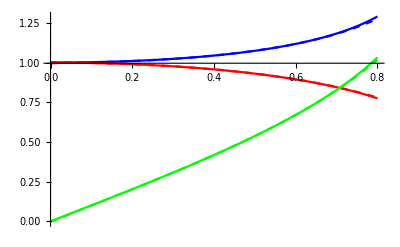

```mathematica
(* terms of the form γ1, γ2 and γ3 do not evaluate *)
γ1 = (1-ρ^2)^(-1/4);
γ2 = (1-ρ^2)^(1/4);
γ3 = ρ(1-ρ^2)^(-1/4);

(* Here we test the expansion order for a NA = 0.8. Taylor expansions about zero are poor, so we take expansions about the midpoint instead, although this is somewhat arbitrary *)
ρLim =0.8;
ord = 5;
cen = ρLim/2;

γseries1 = Normal[Series[γ1, {ρ,cen,ord}]];
γseries2 = Normal[Series[γ2, {ρ,cen,ord}]];
γseries3 = Normal[Series[γ3, {ρ,cen,ord}]];

p1 = Plot[{γ1, γseries1}, {ρ,0, ρLim}, PlotStyle->{{Blue, Dashing[None]}, {Blue, Dashed}}, PlotRange->All];
p2 = Plot[{ γ2, γseries2}, {ρ,0, ρLim}, PlotStyle->{{Red, Dashing[None]}, {Red, Dashed}}, PlotRange->All];
p3 = Plot[{ γ3, γseries3}, {ρ,0, ρLim}, PlotStyle->{{Green, Dashing[None]}, {Green, Dashed}}, PlotRange->All];
Show[p1,p2, p3,PlotRange->All]
```

For even the highest NAs used in experiments, low order approximations are accurate. For NA < 0.4, even the zeroth order approximation is pretty good. This limit is treated analytically in Araneda (2018) by taking a small angle approximation of the dipole mode, this is equivalent to taking the zeroth order expansion about ρ=0.

```mathematica
(* This is the Greens function for a NA of ρLim, with γ substitutions up to the Taylor series order ord, giving our truncated Hankel transform of order ord *)
Clear[ord, ρLim, GIser, GIprox]
GIser[ρLim_,n_]:= Sum[Exp[I θ l]2 Pi I^(-l)Integrate[ 
SeriesCoefficient[
FourierCoefficient[GF, θ, l]
,{ρ, ρLim/2, n}]
ρ (ρ -ρLim/2)^n BesselJ[l, ρ r], {ρ, ρLim/2, ρLim}],
{l,-2,2}];
GIprox[ρLim_, ord_] := Total[ParallelTable[ GIser[ρLim, n], {n, 0 , ord}]];
```

```mathematica
(* zeroth order approximation, for example*)
MatrixForm[FullSimplify[GIprox[0.1,0]]]
```

((-0.314159 BesselJ[1.,0.05 r]+0.628319 BesselJ[1.,0.1 r])/r | (ⅇ^(-2 ⅈ θ) (8.73059×10^-19+0.00786382 BesselJ[0.,0.05 r]-0.00786382 BesselJ[0.,0.1 r]+0.000196595 r BesselJ[1.,0.05 r]-0.000393191 r BesselJ[1.,0.1 r]))/r^2 | 2 ⅈ ⅇ^(-ⅈ θ) π (5.89625×10^-6 r HypergeometricPFQ[{1.5},{2.,2.5},-0.0025 r^2]-7.37031×10^-7 r HypergeometricPFQ[{1.5},{2.,2.5},-0.000625 r^2])
(ⅇ^(2 ⅈ θ) (8.73059×10^-19+0.00786382 BesselJ[0.,0.05 r]-0.00786382 BesselJ[0.,0.1 r]+0.000196595 r BesselJ[1.,0.05 r]-0.000393191 r BesselJ[1.,0.1 r]))/r^2 | (-0.314159 BesselJ[1.,0.05 r]+0.628319 BesselJ[1.,0.1 r])/r | (0.+0.0000370472 ⅈ) ⅇ^(ⅈ θ) r (1. HypergeometricPFQ[{1.5},{2.,2.5},-0.0025 r^2]-0.125 HypergeometricPFQ[{1.5},{2.,2.5},-0.000625 r^2])
0 | 0 | 0)

Before moving forward, we satisfy ourselves that the truncated Hankel approximation to the Greens function converges appropriately. We note that the approximate Greens function is discontinuous at r=0. The function conPlot[i,j] plots the [i,j] term of the approximate Greens function along a slice at θPlot as the order increases from 0 to ord (dark to bright). We show the convergence plot for each term of the Green’s function.

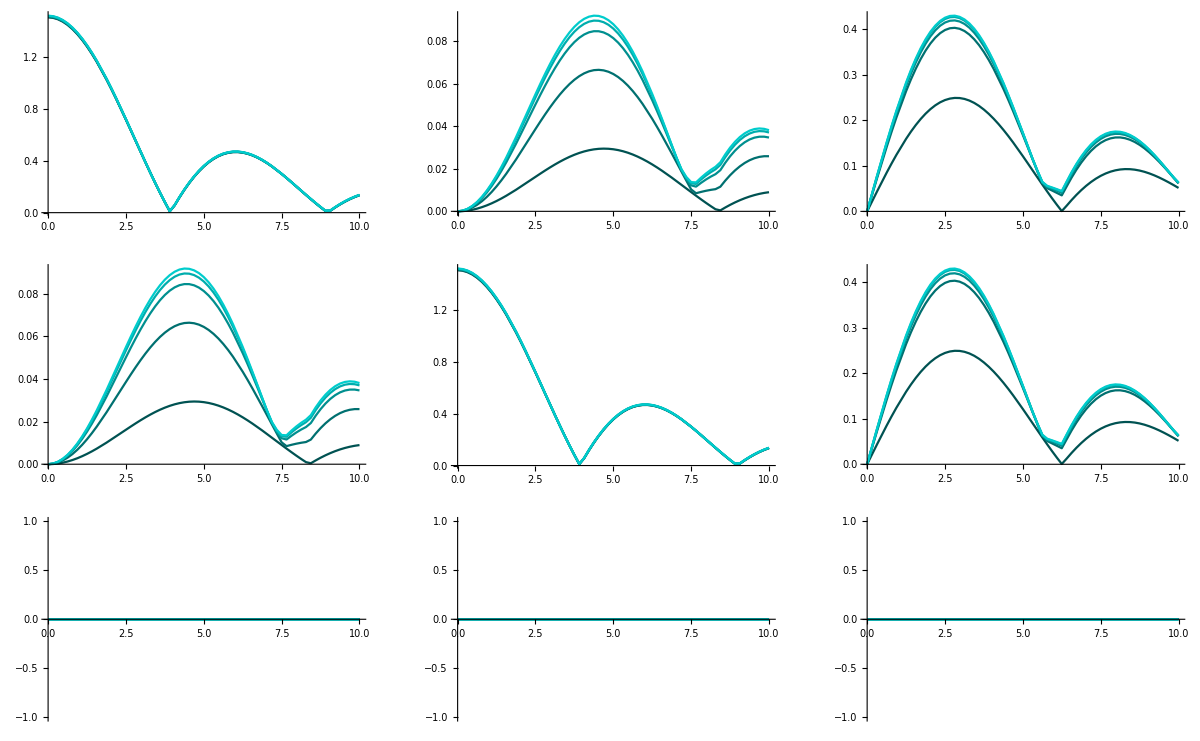

```mathematica
(* we test convergence for NA = 0.8 up to 5th order *)
ρLim=0.8;
ord = 5;
θPlot = 0;

Clear[con]
conPlot[i_,j_] := 
Block[{},
con = Accumulate[ParallelTable[ FullSimplify[Abs[ GIser[ρLim,n][[i,j]]/.θ->θPlot ]], {n, 0 , ord}]];
pTab = ParallelTable[Plot[Abs[con[[k ]]], {r,0.001,10}, PlotStyle->  Hue[0.5, 1, (1 + 3*k/ord)/5 ,1], PlotRange->All, PlotPoints->2],{k,1,ord}];
Show[pTab]
]

GraphicsGrid[ Table[conPlot[i,j],{i,1,3},{j,1,3}]]
```

## Approximate image plane Greens functions for plots

Now that we’ve satisfied ourselves that the approximate Greens function converges satisfactorily, we define the approximate Greens function to use in further calculations (using orders appropriate for each NA).

```mathematica
(* Define parameters for approximate Greens functions *)
NA1=0.6;
ord1 = 2;

NA2= 0.3;
ord2 = 1;

(* we define two approximate greens functions for two numerical apertures *)
GIprox1 = Total[ParallelTable[ GIser[NA1, n], {n, 0 ,ord1}]];
GIprox2 = Total[ParallelTable[ GIser[NA2, n], {n, 0 ,ord2}]];

(* image plane limit for plots *)
rLim=15;
```

## Centre of mass of dipole image

The centre of mass of the dipole image may be displaced by spin-orbit coupling in the dipole field. This function calculates the centre of mass displacement as a function of the mixing angle α for a set of dipoles made by superposing z and y linear dipoles. Because this elliptical dipole has x reflection symmetry (see the fields to follow) we calculate the y displacement over only half of the image.

We define two methods of centroid finding, one brute force method using parallel processing over a grid and one using Mathematica’s (much smarter) numerical integration tool.

```mathematica
(* Find centroid of image for d(α) given Greens function GIprox using brute force *)
getCM1[α_, GIprox_, lim_, res_]:=
Block[{},
(* elliptical dipole parametized by mixing angle α *)
dip = Sqrt[3/(8Pi)]Vdag.{0,Cos[α Pi],I Sin[α Pi]};

(* Calculate dipole image *)
EI = GIprox.dip;
IntI =Conjugate[EI].EI;
l4 = ParallelTable[{r Abs[IntI],r^2 Sin[θ]Abs[IntI]}, {r,0.01,lim, lim/res}, {θ,-π/2,π/2, π/res}];

(* calculate centre of mass *)
ts = Total[Chop[Flatten[l4,1]],{1}] ;
cm = ts[[2]]/ts[[1]]
]


(* Find centroid of image for d(α) given Greens function GIprox using Mathematica's numerical integration package *)
getCM2[α_, GIprox_, lim_, prec_]:=
Block[{},

(* general dipole *)
dip =  Sqrt[3/(8Pi)]Vdag.{0,Cos[Pi α], I Sin[Pi α]};
EI = GIprox.dip;
Int =Conjugate[EI].EI;

(* total intensity *)
tInt = Quiet@NIntegrate[r Abs[Int], {r,0.01,lim}, {θ,-π/2, π/2}, PrecisionGoal->prec, AccuracyGoal->prec];

(* centre of mass *)
cm = Quiet@NIntegrate[r^2 Sin[θ] Abs[Int], {r,0.01, lim}, {θ,-π/2, π/2}, PrecisionGoal->prec, AccuracyGoal->prec]/tInt 
]
```

```mathematica
(* test cm functions over three dipoles and compare calculation times *)
```

```mathematica
Timing[cm1 = getCM2[0, GIprox2, 25/0.3,4];
cm2 =getCM2[0.25, GIprox2, 25/0.3,4];
cm3 =getCM2[0.4, GIprox2, 25/0.3,4];
Grid[{{cm1,cm2,cm3}}]]
```

{31.3301,-3.0848×10^-16 | -0.9763 | -2.06538}

```mathematica
Timing[cm1 = getCM1[0, GIprox2, 25/0.3,100];
cm2 =getCM1[0.25, GIprox2, 25/0.3,100];
cm3 =getCM1[0.4, GIprox2, 25/0.3,100];
Grid[{{cm1,cm2,cm3}}]]
```

{19.4723,-5.46619×10^-17 | -0.987018 | -2.08687}

getCM1 is approximately correct for high resolutions (>100)

## Plotting functions for fields in Fourier and image planes

Here we define plotting functions for displaying the fields as hue/intensity plots. We define two types of hue/intensity plots: with and without weighting by field intensity. 

Image plane fields are plotted using ParallelTable and ListDensityPlot.

To export nicely, the field plots are rasterized and vector axes are superimposed over the top.

```mathematica
sca = 1.395 (* one of the printer functions introduces this scale *)
imSiz = sca*toPrintPoints[Quantity[18.5, "mm"]];
pad = sca*{{0,0}, {0,0}}; (*image padding *)
rpad=0.02; (* range padding *);
dash = sca*0.02

(* resolution controls *)
ppoints = 100;
res = 600;


(* phasePlot1 shows phase with normalization *)
phasePlot1[f_,norm_,range_,r1_, r2_,opts:OptionsPattern[]]:= Overlay[{
Rasterize[RegionPlot[x^2+y^2<range^2,{x,-range,range},{y,-range,range},opts,PlotPoints->ppoints,ColorFunctionScaling->False,ColorFunction->Function[{x,y},Hue[Arg[f[x,y]]/(2 Pi)+1/2,1, 0.8,Norm[f[x,y]]^2   /norm  ]], Frame->False, BoundaryStyle->None, Axes->False,
ImageSize->imSiz, PlotRangePadding->rpad, ImagePadding->pad], RasterSize->res],
Show[
Graphics[{AbsoluteThickness[sca*0.7],Circle[{0,0},1]}],
Graphics[{AbsoluteThickness[sca*0.7],  Dashing[dash],Circle[{0,0},r1]}],
Graphics[{AbsoluteThickness[sca*0.7],  Dashing[dash],Circle[{0,0},r2]}], 
ImageSize-> imSiz, PlotRangePadding-> rpad, ImagePadding->pad ]
}]

(* phasePlot2 shows phase without normalization *)
phasePlot2[f_,norm_,range_,r1_,r2_,opts:OptionsPattern[]]:= Overlay[{
Rasterize[RegionPlot[x^2+y^2<range^2,{x,-range,range},{y,-range,range},opts,PlotPoints->ppoints,ColorFunctionScaling->False,ColorFunction->Function[{x,y},Hue[Arg[f[x,y]]/(2 Pi)+1/2,1, 0.8,0.8]], Frame->False, BoundaryStyle->None, Axes->False,
ImageSize->imSiz, PlotRangePadding->rpad, ImagePadding->pad], RasterSize->res],
Show[
Graphics[{AbsoluteThickness[sca*0.7],Circle[{0,0},1]}],
Graphics[{AbsoluteThickness[sca*0.7],  Dashing[dash],Circle[{0,0},r1]}],
Graphics[{AbsoluteThickness[sca*0.7],  Dashing[dash],Circle[{0,0},r2]}], 
ImageSize-> imSiz, PlotRangePadding-> rpad, ImagePadding->pad ]
}]

(*Parallel intensity plot - Image plane*)
intPlot2[list_,range_,opts:OptionsPattern[]]:= Quiet@Overlay[{
Rasterize[
ListDensityPlot[list,Frame->False,  PlotRange->All,
PlotRangePadding->rpad,ImageSize->imSiz, ImagePadding->pad]
, RasterSize->res],
Show[
Graphics[{AbsoluteThickness[sca*0.7],Circle[{0,0},range]}],
ImageSize->imSiz, ImagePadding->pad, PlotRangePadding-> rpad]
}]

(* Parallel intensity plot - Fourier plane *)
intPlot3[list_,range_,r1_, r2_,pts:OptionsPattern[]]:= Overlay[{
Rasterize[
ListDensityPlot[list,Frame->False, ColorFunctionScaling->False, PlotRange->All,PlotRangePadding->rpad,
ImageSize->imSiz, ImagePadding->pad], RasterSize->res],
Show[
Graphics[{AbsoluteThickness[sca*0.7],Circle[{0,0},1]}],
Graphics[{AbsoluteThickness[sca*0.7],  Dashing[dash],Circle[{0,0},r1]}],
Graphics[{AbsoluteThickness[sca*0.7],  Dashing[dash],Circle[{0,0},r2]}],
ImageSize-> imSiz, PlotRangePadding-> rpad, ImagePadding->pad ]
}]
```

1.395

0.0279

## Combined plotting function

This function displays several field plots as a row, figures of this type appear in Higginbottom (2018) and Araneda (2018)

```mathematica
listres = 200;

(* Select which Fourier plane projection *)
rule1 = lensRule1;
rule2 = lensRule2;

(* Fourier plane distribution depending on projection *)
Aplot = D[ϕ/.rule2, ρ]*Sin[ϕ/.rule2]/ρ;
GFplot =  FullSimplify[Sqrt[Aplot]( P.Ucdag )/.rule2];

(* Select which plot, with or without intensity normalization *)
phasePlot = phasePlot2;

MakeRow[dip_,normF_, normI_, limF_, limI_, r1_, r2_]:=Block[{},
(* heads is a boolean that switches the text headings on and off *)
EF = GFplot.dip;
(* Fourier plane Intensity plot *)
IntF =(Conjugate[EF].EF//.rule2)/normF;
l1 = Table[{ρ Cos[θ],ρ Sin[θ],IntF}, {ρ,0.01,limF, limF/listres}, {θ,0,2π, π/20}]; p1 = intPlot3[Flatten[l1,1],limF,r1,r2 ];
(* Fourier plane Phase plots L/R*)
func1[x_,y_] :=EF[[1]]//.rule1[x,y]; p2 =phasePlot[func1, normF, limF,r1,r2 ];
func2[x_,y_] :=EF[[2]]//.rule1[x,y];p3 =phasePlot[func2, normF, limF,r1,r2 ];
(* Fourier plane Phase plots H/V*)
func1[x_,y_] :=(V.EF)[[1]]//.rule1[x,y]; p4 =phasePlot[func1, normF, limF,r1,r2 ];
func2[x_,y_] :=(V.EF)[[2]]//.rule1[x,y];p5 =phasePlot[func2, normF, limF,r1,r2 ];

(* Image plane Intensity plot - high aperture *)
EI = GItot.dip;
IntI =Conjugate[EI].EI;
l4 = ParallelTable[{r Cos[θ],r Sin[θ],IntI}, {r,0.0001,limI*1.01, limI/listres}, {θ,0,2π, 2π/listres}]; p8 = intPlot2[Flatten[l4,1], limI];

(* Image plane Intensity plot - NA1 *)
EI = GIprox1.dip;
IntI =Conjugate[EI].EI;
l4 = ParallelTable[{r Cos[θ],r Sin[θ],IntI}, {r,0.1,limI*1.01, limI/listres}, {θ,0,2π, 2π/listres}];p7 = intPlot2[Flatten[l4,1], limI];
(* Image plane Intensity plot - NA2 *)
EI = GIprox2.dip;
IntI =Conjugate[EI].EI;
l4 = ParallelTable[{r Cos[θ],r Sin[θ],IntI}, {r,0.1,limI*1.01, limI/listres}, {θ,0,2π, 2π/listres}]; p6 = intPlot2[Flatten[l4,1], limI];

(* this is the output *)
{" ",p1,p2, p3, p4, p5,Spacer[7], p6, p7,p8}
]
```

## Plot test row

Test the row plotting function for the circular dipole

```mathematica
(* aperture limits depending on projection *)
ρLim1 = ρ/.Solve[(ϕ/.rule2) == ArcSin[NA1], ρ][[1]];
ρLim2 = ρ/.Solve[(ϕ/.rule2) == ArcSin[NA2], ρ][[1]];

normF = 2.5;
α = 0.5 π;
row1 = MakeRow[Vdag.{0,Cos[α], I Sin[α]}, normF,3,0.999, 15, ρLim1, ρLim2]
```

{ ,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-,,-Graphics--Graphics-,-Graphics--Graphics-,-Graphics--Graphics-}

## Maximum displacement for NA1 and NA2

We calculate the dipole that yields a maximally displaced image centroid for NA1 and NA2

```mathematica
Clear[α]
(* maximally displaced dipole for NA1 = 0.6 *)
αmax1 = α/.NMaximize[{-getCM1[α, GIprox1, 30/0.6,50],{α≥ 0.25, α ≤ 0.5}}, α][[2,1]]
(* maximally displaced dipole for NA2 = 0.3 *)
αmax2 = α/.NMaximize[{-getCM1[α,GIprox2, 30/0.3,50],{α≥ 0.25, α ≤ 0.5}}, α][[2,1]]
```

0.351191

0.424947

## Calculate elliptical dipole distributions - Higginbottom (2018) Chap. 7

Now we calculate fields and generate a figure for Higginbottom (2018) Chap. 7. This figure is prepared at high resolution and takes some time to calculate.

```mathematica
(* aperture limits depending on projection *)
ρLim1 = ρ/.Solve[(ϕ/.rule2) == ArcSin[NA1], ρ][[1]];
ρLim2 = ρ/.Solve[(ϕ/.rule2) == ArcSin[NA2], ρ][[1]];

limI=20;

normF = 2.5;

α = 0;
row1 = MakeRow[Vdag.{0,Cos[α], I Sin[α]}, normF,3,0.999, limI, ρLim1, ρLim2];

α = 0.15 π;
row2 = MakeRow[Vdag.{0,Cos[α], I Sin[α]}, normF,3,0.999, limI, ρLim1, ρLim2];

α = 0.25 π;
row3 = MakeRow[Vdag.{0,Cos[α], I Sin[α]}, normF,3,0.999, limI, ρLim1, ρLim2];

α = αmax1 π;
row4 = MakeRow[Vdag.{0,Cos[α], I Sin[α]}, normF,3,0.999, limI, ρLim1, ρLim2];

α = αmax2 π;
row5 = MakeRow[Vdag.{0,Cos[α], I Sin[α]}, normF,3,0.999, limI, ρLim1, ρLim2];

α =0.5 π;
row6 = MakeRow[Vdag.{0,Cos[α], I Sin[α]}, normF,3,0.999, limI, ρLim1, ρLim2];
```

```mathematica
heads = MaTeX[{"","I" , "E_R", "E_L", "E_H","E_V" ,"", "I'(\\mathrm{NA}=0.3)", "I'(\\mathrm{NA}=0.6)" , "I'(\\mathrm{NA}=1.0)"}];
grid = {heads,row1,row2, row3, row4, row5,row6};

(* row headings *)
labs = Rotate[#,90 Degree]&/@MaTeX[ {"",
"\\vec{d}(\\alpha/\\pi = 0.00)",
"\\vec{d}(\\alpha/\\pi = 0.15)",
"\\vec{d}(\\alpha/\\pi = 0.25)",
"\\vec{d}(\\alpha/\\pi = 0.35)",
"\\vec{d}(\\alpha/\\pi = 0.42)",
"\\vec{d}(\\alpha/\\pi = 0.50)"
}, FontSize->sca*8] ;
grid[[;;,1]] = labs;
```

```mathematica
Grid[grid]
outlinedGraphics=First@ImportString[ExportString[%,"PDF"],"PDF","TextMode"->"Outlines"]
Export["CombinedDipoles.pdf",%];
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- |  | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- |  | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- |  | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- |  | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- |  | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- |  | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-

-Graphics-

## Calculate dipole distributions - Araneda (2018) version

Repeating the same process with a slightly different selection of dipoles for Araneda (2018) .

```mathematica
(* aperture limits depending on projection *)
ρLim1 = ρ/.Solve[(ϕ/.rule2) == ArcSin[NA1], ρ][[1]];
ρLim2 = ρ/.Solve[(ϕ/.rule2) == ArcSin[NA2], ρ][[1]];

limI=20;

normF = 2.5;
row1 = MakeRow[{1,0,0}, normF,3,0.999, limI, ρLim1, ρLim2];
row2 = MakeRow[Vdag.{0,1,0}, normF,3,0.999, limI, ρLim1, ρLim2]; (* y dipole *)

(* Almost maximally displaced NA = 0.6 dipole *)
ϵ = 0.5
α = ArcTan[ϵ];
row3 = MakeRow[Vdag.{0,Cos[α], I Sin[α]}, normF,3,0.999, limI, ρLim1, ρLim2];

ϵ = 1
α = ArcTan[ϵ];
row4 = MakeRow[Vdag.{0,Cos[α], I Sin[α]}, normF,3,0.999, limI, ρLim1, ρLim2];

(* Almost maximally displaced NA = 0.3 dipole *)
ϵ = 2;
α = ArcTan[ϵ];
row5 = MakeRow[Vdag.{0,Cos[α], I Sin[α]}, normF,3,0.999, limI, ρLim1, ρLim2];

row6 = MakeRow[{0,0,I}, 3,3,0.999, limI, ρLim1, ρLim2];
```

0.5

1

```mathematica
heads = MaTeX[{"","I" , "E_R", "E_L", "E_H","E_V" ,"", "I'(\\mathrm{NA}=1.0)", "I'(\\mathrm{NA}=0.6)" , "I'(\\mathrm{NA}=0.3)"}];
grid = {heads,row1, {" "},row2, row3, row4, row5,row6};

(* row headings *)
labs = Rotate[#,90 Degree]&/@MaTeX[ {"",
"\\vec{d} = \\vec{\\sigma}^+_z",
"",
"\\vec{d}(\\epsilon = 0)",
"\\vec{d}(\\epsilon = 0.5)",
"\\vec{d}(\\epsilon = 1)",
"\\vec{d}(\\epsilon = 2)",
"\\vec{d}(\\epsilon = \\infty)"
}, FontSize->sca*8] ;
grid[[;;,1]] = labs;
```

```mathematica
Grid[grid]
outlinedGraphics=First@ImportString[ExportString[%,"PDF"],"PDF","TextMode"->"Outlines"]
Export["CombinedDipoles.pdf",%];
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- |  | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics- |  |  |  |  |  |  |  |  | 
-Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- |  | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- |  | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- |  | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- |  | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- |  | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-

-Graphics-

## Colorbar

```mathematica
Show[RegionPlot[x>0,{x,0,1},{y,0,0.01},PlotPoints->20,ColorFunctionScaling->True,ColorFunction->Function[{x,y},approximateDefaultColorFunction[x]], Frame->True, BoundaryStyle->Directive[Black, AbsoluteThickness[0.4]], ImageSize->toPrintPoints[Quantity[35, "mm"]], Axes->False, AspectRatio->0.07, FrameTicks-> None, Axes->False, PlotRangePadding->0, Axes->False], FrameTicks->{None, None, None, None}, FrameStyle->Directive[Black, AbsoluteThickness[0.4]]]
Export["colorbar.png",%, ImageResolution->res]
```

-Graphics-

colorbar.png

## Displacement as a function of ellipticity and NA

We define a function that uses an appropriate order approximation for a each NA, but for NA =1 we will use the exact analytic solution.

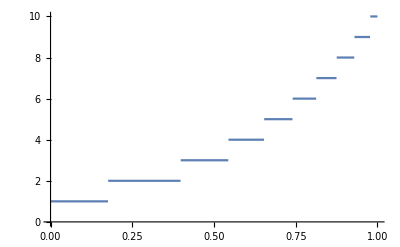

```mathematica
ord = Round[10^a];
Plot[ord, {a,0,1}]

(* list of apertures to test *)
alist = Table[aloop, {aloop,0.1,1.0,0.1}];
(* pre calculate approximate greens functions to save time *)
GIlist = ParallelTable[
aloop = alist[[i]];
If[aloop==1, GItot,FullSimplify[Total[Table[ GIser[aloop, n], {n, 0 ,ord/.a->aloop}]], Assumptions->Re[r]>0]], 
{i, 1, Length[alist],1}];
```

```mathematica
(* check elements of GIlist *)
MatrixForm@GIlist[[9]]
```

((-105.122 BesselJ[5.,0.45 r]+3363.9 BesselJ[5.,0.9 r]+r (-121.723 BesselJ[4.,0.45 r]+1947.56 BesselJ[4.,0.9 r]+r (-18.5449 BesselJ[3.,0.45 r]+148.359 BesselJ[3.,0.9 r]+17.2416 BesselJ[5.,0.45 r]-892.327 BesselJ[5.,0.9 r]+r (-0.699203 BesselJ[2.,0.45 r]+2.79681 BesselJ[2.,0.9 r]+3.0811 BesselJ[4.,0.45 r]-197.19 BesselJ[4.,0.9 r]+r (-2.81164 BesselJ[1.,0.45 r]+5.62328 BesselJ[1.,0.9 r]+0.626739 BesselJ[3.,0.45 r]-16.2799 BesselJ[3.,0.9 r]-0.242308 BesselJ[5.,0.45 r]+35.3261 BesselJ[5.,0.9 r])-0.0997836 BesselJ[6.,0.45 r]+25.5446 BesselJ[6.,0.9 r])))+r^5 (0.0186002 HypergeometricPFQ[{},{2.},-0.2025 r^2]-0.00465005 HypergeometricPFQ[{},{2.},-0.050625 r^2]-0.050102 HypergeometricPFQ[{1.5},{1.,2.5},-0.2025 r^2]+0.00626275 HypergeometricPFQ[{1.5},{1.,2.5},-0.050625 r^2]-0.982104 HypergeometricPFQ[{2.5},{1.,3.5},-0.2025 r^2]+0.0306907 HypergeometricPFQ[{2.5},{1.,3.5},-0.050625 r^2]-3.3858 HypergeometricPFQ[{3.5},{1.,4.5},-0.2025 r^2]+0.0264515 HypergeometricPFQ[{3.5},{1.,4.5},-0.050625 r^2]-1.92431 HypergeometricPFQ[{4.5},{1.,5.5},-0.2025 r^2]+0.00375842 HypergeometricPFQ[{4.5},{1.,5.5},-0.050625 r^2]))/r^5 | (ⅇ^(-2 ⅈ θ) (1.65913×10^-16 r^2-107.129 BesselJ[6.,0.45 r]+6856.28 BesselJ[6.,0.9 r]+r (-98.0454 BesselJ[5.,0.45 r]+3137.45 BesselJ[5.,0.9 r]+4.41909 BesselJ[7.,0.45 r]-565.643 BesselJ[7.,0.9 r]+r (0.0383012 BesselJ[0.,0.45 r]-0.0383012 BesselJ[0.,0.9 r]-11.2337 BesselJ[4.,0.45 r]+179.74 BesselJ[4.,0.9 r]+4.30944 BesselJ[6.,0.45 r]-397.289 BesselJ[6.,0.9 r]+r (0.00861776 BesselJ[1.,0.45 r]-0.0172355 BesselJ[1.,0.9 r]+1.25616 BesselJ[5.,0.45 r]-79.9054 BesselJ[5.,0.9 r]-0.0203378 BesselJ[7.,0.45 r]+10.413 BesselJ[7.,0.9 r])))+r^6 (0.0512598 HypergeometricPFQ[{},{4.},-0.2025 r^2]-0.000800935 HypergeometricPFQ[{},{4.},-0.050625 r^2]-0.00538636 HypergeometricPFQ[{2.5},{3.,3.5},-0.2025 r^2]+0.000168324 HypergeometricPFQ[{2.5},{3.,3.5},-0.050625 r^2]-0.126037 HypergeometricPFQ[{3.5},{3.,4.5},-0.2025 r^2]+0.000984667 HypergeometricPFQ[{3.5},{3.,4.5},-0.050625 r^2]-0.475052 HypergeometricPFQ[{4.5},{3.,5.5},-0.2025 r^2]+0.000927836 HypergeometricPFQ[{4.5},{3.,5.5},-0.050625 r^2]-0.286015 HypergeometricPFQ[{5.5},{3.,6.5},-0.2025 r^2]+0.000139656 HypergeometricPFQ[{5.5},{3.,6.5},-0.050625 r^2])))/r^4 | -((0.+0.355866 ⅈ) ⅇ^(-ⅈ θ) (-926.113 BesselJ[5.,0.45 r]+29635.6 BesselJ[5.,0.9 r]+r (-282.425 BesselJ[4.,0.45 r]+4518.8 BesselJ[4.,0.9 r]+52.0938 BesselJ[6.,0.45 r]-3334.01 BesselJ[6.,0.9 r]+r (-16.4692 BesselJ[3.,0.45 r]+131.754 BesselJ[3.,0.9 r]+20.3585 BesselJ[5.,0.45 r]-1589.16 BesselJ[5.,0.9 r]+r (3.01494 BesselJ[2.,0.45 r]-12.0598 BesselJ[2.,0.9 r]+4.23575 BesselJ[4.,0.45 r]-182.154 BesselJ[4.,0.9 r]-0.439542 BesselJ[6.,0.45 r]+112.523 BesselJ[6.,0.9 r]+r^2 (1. Hypergeometric0F1Regularized[3.,-0.2025 r^2]-0.0625 Hypergeometric0F1Regularized[3.,-0.050625 r^2]))))+r^5 (-0.204866 HypergeometricPFQ[{},{3.},-0.2025 r^2]+0.0128041 HypergeometricPFQ[{},{3.},-0.050625 r^2]-0.00762009 HypergeometricPFQ[{1.5},{2.,2.5},-0.2025 r^2]+0.000952511 HypergeometricPFQ[{1.5},{2.,2.5},-0.050625 r^2]-0.591373 HypergeometricPFQ[{2.5},{2.,3.5},-0.2025 r^2]+0.0184804 HypergeometricPFQ[{2.5},{2.,3.5},-0.050625 r^2]-5.01748 HypergeometricPFQ[{3.5},{2.,4.5},-0.2025 r^2]+0.0391991 HypergeometricPFQ[{3.5},{2.,4.5},-0.050625 r^2]-7.76028 HypergeometricPFQ[{4.5},{2.,5.5},-0.2025 r^2]+0.0151568 HypergeometricPFQ[{4.5},{2.,5.5},-0.050625 r^2]-1.24793 HypergeometricPFQ[{5.5},{2.,6.5},-0.2025 r^2]+0.000609339 HypergeometricPFQ[{5.5},{2.,6.5},-0.050625 r^2])))/r^4
(ⅇ^(2 ⅈ θ) (1.65913×10^-16 r^2-107.129 BesselJ[6.,0.45 r]+6856.28 BesselJ[6.,0.9 r]+r (-98.0454 BesselJ[5.,0.45 r]+3137.45 BesselJ[5.,0.9 r]+4.41909 BesselJ[7.,0.45 r]-565.643 BesselJ[7.,0.9 r]+r (0.0383012 BesselJ[0.,0.45 r]-0.0383012 BesselJ[0.,0.9 r]-11.2337 BesselJ[4.,0.45 r]+179.74 BesselJ[4.,0.9 r]+4.30944 BesselJ[6.,0.45 r]-397.289 BesselJ[6.,0.9 r]+r (0.00861776 BesselJ[1.,0.45 r]-0.0172355 BesselJ[1.,0.9 r]+1.25616 BesselJ[5.,0.45 r]-79.9054 BesselJ[5.,0.9 r]-0.0203378 BesselJ[7.,0.45 r]+10.413 BesselJ[7.,0.9 r])))+r^6 (0.0512598 HypergeometricPFQ[{},{4.},-0.2025 r^2]-0.000800935 HypergeometricPFQ[{},{4.},-0.050625 r^2]-0.00538636 HypergeometricPFQ[{2.5},{3.,3.5},-0.2025 r^2]+0.000168324 HypergeometricPFQ[{2.5},{3.,3.5},-0.050625 r^2]-0.126037 HypergeometricPFQ[{3.5},{3.,4.5},-0.2025 r^2]+0.000984667 HypergeometricPFQ[{3.5},{3.,4.5},-0.050625 r^2]-0.475052 HypergeometricPFQ[{4.5},{3.,5.5},-0.2025 r^2]+0.000927836 HypergeometricPFQ[{4.5},{3.,5.5},-0.050625 r^2]-0.286015 HypergeometricPFQ[{5.5},{3.,6.5},-0.2025 r^2]+0.000139656 HypergeometricPFQ[{5.5},{3.,6.5},-0.050625 r^2])))/r^4 | (-105.122 BesselJ[5.,0.45 r]+3363.9 BesselJ[5.,0.9 r]+r (-121.723 BesselJ[4.,0.45 r]+1947.56 BesselJ[4.,0.9 r]+r (-18.5449 BesselJ[3.,0.45 r]+148.359 BesselJ[3.,0.9 r]+17.2416 BesselJ[5.,0.45 r]-892.327 BesselJ[5.,0.9 r]+r (-0.699203 BesselJ[2.,0.45 r]+2.79681 BesselJ[2.,0.9 r]+3.0811 BesselJ[4.,0.45 r]-197.19 BesselJ[4.,0.9 r]+r (-2.81164 BesselJ[1.,0.45 r]+5.62328 BesselJ[1.,0.9 r]+0.626739 BesselJ[3.,0.45 r]-16.2799 BesselJ[3.,0.9 r]-0.242308 BesselJ[5.,0.45 r]+35.3261 BesselJ[5.,0.9 r])-0.0997836 BesselJ[6.,0.45 r]+25.5446 BesselJ[6.,0.9 r])))+r^5 (0.0186002 HypergeometricPFQ[{},{2.},-0.2025 r^2]-0.00465005 HypergeometricPFQ[{},{2.},-0.050625 r^2]-0.050102 HypergeometricPFQ[{1.5},{1.,2.5},-0.2025 r^2]+0.00626275 HypergeometricPFQ[{1.5},{1.,2.5},-0.050625 r^2]-0.982104 HypergeometricPFQ[{2.5},{1.,3.5},-0.2025 r^2]+0.0306907 HypergeometricPFQ[{2.5},{1.,3.5},-0.050625 r^2]-3.3858 HypergeometricPFQ[{3.5},{1.,4.5},-0.2025 r^2]+0.0264515 HypergeometricPFQ[{3.5},{1.,4.5},-0.050625 r^2]-1.92431 HypergeometricPFQ[{4.5},{1.,5.5},-0.2025 r^2]+0.00375842 HypergeometricPFQ[{4.5},{1.,5.5},-0.050625 r^2]))/r^5 | -((0.+0.355866 ⅈ) ⅇ^(ⅈ θ) (-926.113 BesselJ[5.,0.45 r]+29635.6 BesselJ[5.,0.9 r]+r (-282.425 BesselJ[4.,0.45 r]+4518.8 BesselJ[4.,0.9 r]+52.0938 BesselJ[6.,0.45 r]-3334.01 BesselJ[6.,0.9 r]+r (-16.4692 BesselJ[3.,0.45 r]+131.754 BesselJ[3.,0.9 r]+20.3585 BesselJ[5.,0.45 r]-1589.16 BesselJ[5.,0.9 r]+r (3.01494 BesselJ[2.,0.45 r]-12.0598 BesselJ[2.,0.9 r]+4.23575 BesselJ[4.,0.45 r]-182.154 BesselJ[4.,0.9 r]-0.439542 BesselJ[6.,0.45 r]+112.523 BesselJ[6.,0.9 r]+r^2 (1. Hypergeometric0F1Regularized[3.,-0.2025 r^2]-0.0625 Hypergeometric0F1Regularized[3.,-0.050625 r^2]))))+r^5 (-0.204866 HypergeometricPFQ[{},{3.},-0.2025 r^2]+0.0128041 HypergeometricPFQ[{},{3.},-0.050625 r^2]-0.00762009 HypergeometricPFQ[{1.5},{2.,2.5},-0.2025 r^2]+0.000952511 HypergeometricPFQ[{1.5},{2.,2.5},-0.050625 r^2]-0.591373 HypergeometricPFQ[{2.5},{2.,3.5},-0.2025 r^2]+0.0184804 HypergeometricPFQ[{2.5},{2.,3.5},-0.050625 r^2]-5.01748 HypergeometricPFQ[{3.5},{2.,4.5},-0.2025 r^2]+0.0391991 HypergeometricPFQ[{3.5},{2.,4.5},-0.050625 r^2]-7.76028 HypergeometricPFQ[{4.5},{2.,5.5},-0.2025 r^2]+0.0151568 HypergeometricPFQ[{4.5},{2.,5.5},-0.050625 r^2]-1.24793 HypergeometricPFQ[{5.5},{2.,6.5},-0.2025 r^2]+0.000609339 HypergeometricPFQ[{5.5},{2.,6.5},-0.050625 r^2])))/r^4
0 | 0 | 0)

```mathematica
(*Displacement by centre of mass*)
Timing[
(* parallel loop at highest level so that the function doesn't wait on slow evaluations *)
table2 = ParallelTable[
aloop = alist[[i]]; 
GIloop = GIlist[[i]];

{aloop, { αloop,
(* get CM by efficient method without parallelization *)
getCM2[αloop, GIloop, 25/aloop, 4]

}}
,{αloop, 0,1, 0.01},{i,1,Length[alist],1} ];]
```

{935.192,Null}

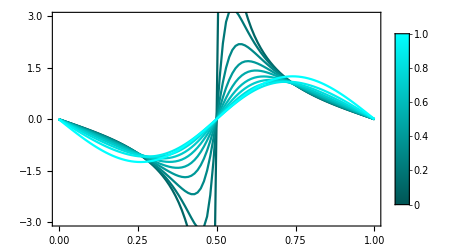

Displacement_alpha.pdf

```mathematica
table3 = Split[Sort[Flatten[table2,1],#1[[1]]<#2[[1]]&],  #1[[1]]===#2[[1]]&];
fun[element_]:= ListPlot[Flatten[Drop[element,0,1],1], Joined->True, PlotStyle->Hue[0.5,1,element[[1,1]]*2/3 + 1/3,1], Frame->True]

cf=Function[x,Hue[0.5,1,x*2/3 + 1/3,1]];
Legended[Show[Map[fun, table3], PlotRange->{-3,3}, PlotRangePadding->0], BarLegend[{cf,{0,1}}]]
Export["Displacement_alpha.pdf",%]
```